```mathematica
raw=Flatten@Import[FileNameJoin[{NotebookDirectory[],"power_130DegreesOnResonance_2.csv"}]];
```

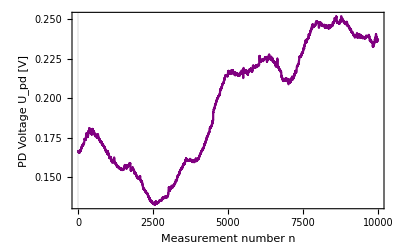

```mathematica
ListLinePlot[raw,PlotStyle->Purple,FrameLabel->Thread[Style[{"Measurement number n","PD Voltage U_pd [V]"},14]],PlotRange->All]
```

```mathematica
fraw=Fourier[raw];
cutF=3000;
data=Re@InverseFourier[fraw[[cutF;;-cutF]]];
data=data-Mean[data];
data/=StandardDeviation[data];
dataC=data;
```

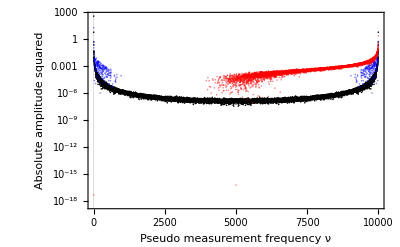

```mathematica
ListLogPlot[{Abs[fraw]^2,Re[fraw],Im[fraw]},PlotStyle->{Black,Opacity[0.5,Blue],Opacity[0.5,Red]},FrameLabel->Thread[Style[{"Pseudo measurement frequency ν","Absolute amplitude squared"},14]]]
```

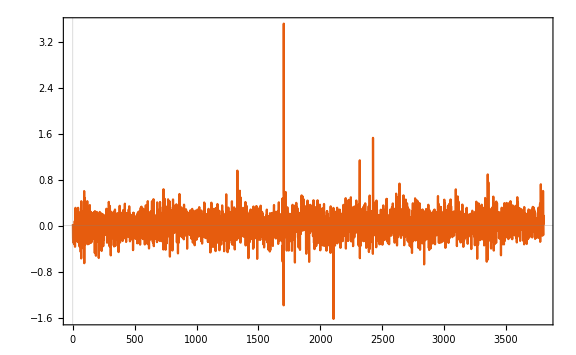

```mathematica
ListLinePlot[dataC[[100;;-100]],PlotRange->All]
```

```mathematica
params=FindDistributionParameters[dataC[[100;;-100]],VoigtDistribution[a,b],{{a,0.05},{b,0.15}}]//Timing
```

{23.9531,{a→0.00345236,b→0.180885}}

```mathematica
dataCRes=DeleteDuplicates@CDF[VoigtDistribution[0.00345236,0.180885],dataC[[100;;-100]]];
```

```mathematica
Length@DeleteDuplicates[dataCRes]
```

8002

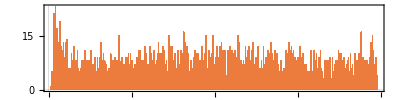

```mathematica
Histogram[dataCRes,500,AspectRatio->1/4]
```

```mathematica
uniformStr=StringJoin[(StringJoin[ToString/@IntegerDigits[Round[#*2^40],2]])&/@(dataCRes)];
```

```mathematica
StringTake[uniformStr,100]
```

1010010111011101000111111111111010100001101111000000001100101111010110111101001011011100111000110101

## electrical noise

```mathematica
raw=Flatten@Import[FileNameJoin[{NotebookDirectory[],"power_electric_noise.csv"}]];
```

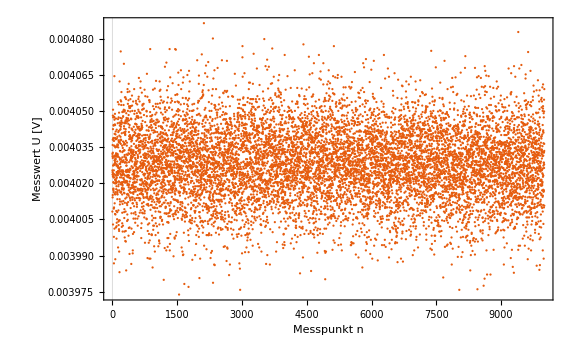

```mathematica
ListPlot[raw,ImageSize->Large,FrameLabel->Thread[Style[{"Messpunkt n","Messwert U [V]"},14]],PlotRange->{{0,10000},All}]
```

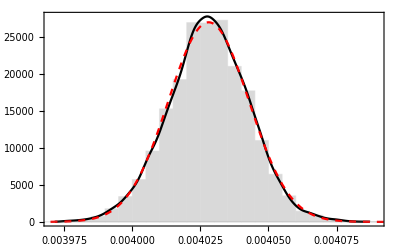

```mathematica
Show[{Histogram[raw,20,"PDF",ChartStyle->LightGray],SmoothHistogram[raw,PlotStyle->Black],Plot[PDF[NormalDistribution[Mean[raw],StandardDeviation[raw]],x],{x,0.00397,0.0045},PlotStyle->Directive[{Dashed,Red}],PlotRange->All]}]
```

```mathematica
data=raw-Mean[raw];
data/=StandardDeviation[data];
uniform=CDF[NormalDistribution[Mean[data],StandardDeviation[data]],data];
uniformStr=StringJoin[(StringJoin[ToString/@IntegerDigits[Round[#],2]])&/@uniform];
```

```mathematica
StringLength[uniformStr]
```

10000

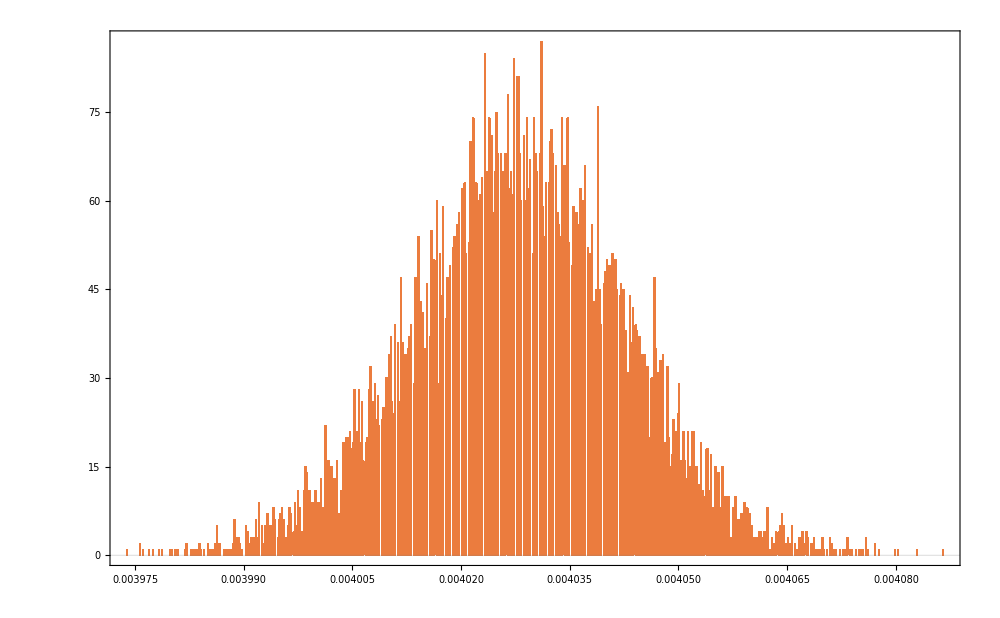

```mathematica
Histogram[raw,500,ImageSize->1000]
```

```mathematica
Length[DeleteDuplicates[raw]]
```

387

```mathematica
Differences[MinMax[raw]]/387
```

{2.91392×10^-7}